TROJITÁ GEOMETRICKÁ TRANSFORMÁCIA DOMČEKA

==========================================

POČIATOČNÝ DOMČEK:

Vrcholy domčeka:

(-2 | 0
2 | 0
2 | 4
-2 | 4
0 | 6)

Vlastnosti domčeka:

Obsah: 20

Obvod: 21

PRVÁ TRANSFORMÁCIA: Posun

GEOMETRICKÉ TRANSFORMÁCIE DOMČEKA - POSUN

========================================

ZADANIE:

Majme domček s vrcholmi:

(-2 | 0
2 | 0
2 | 4
-2 | 4
0 | 6)

Vykonajte posun domčeka v 2D priestore pomocou vektora posunu: Δ = [-3, 5]

Transformačná matica posunu v homogénnych súradniciach:

(1 | 0 | -3
0 | 1 | 5
0 | 0 | 1)

POSTUP:

Pre výpočet použijeme maticu posunu v homogénnych súradniciach:

Transformačná matica:

(1 | 0 | dx
0 | 1 | dy
0 | 0 | 1)

Pre naše hodnoty:

dx = -3

dy = 5

Posun vykonáme pomocou vzorcov:

x' = x + dx

y' = y + dy

Výpočet pre jednotlivé vrcholy:

Vrchol 1:

Pôvodné súradnice: [-2, 0]

Výpočet x-ovej súradnice:

x' = x + dx = -2 + -3

x' = -5

Výpočet y-ovej súradnice:

y' = y + dy = 0 + 5

y' = 5

Overenie pomocou inverznej transformácie:

x = x' + (-dx) = -5 + (3) = -2

y = y' + (-dy) = 5 + (-5) = 0

Maticový zápis:

(1 | 0 | -3
0 | 1 | 5
0 | 0 | 1) · (-2
0
1) = (-5
5
1)

Vrchol 2:

Pôvodné súradnice: [2, 0]

Výpočet x-ovej súradnice:

x' = x + dx = 2 + -3

x' = -1

Výpočet y-ovej súradnice:

y' = y + dy = 0 + 5

y' = 5

Overenie pomocou inverznej transformácie:

x = x' + (-dx) = -1 + (3) = 2

y = y' + (-dy) = 5 + (-5) = 0

Maticový zápis:

(1 | 0 | -3
0 | 1 | 5
0 | 0 | 1) · (2
0
1) = (-1
5
1)

Vrchol 3:

Pôvodné súradnice: [2, 4]

Výpočet x-ovej súradnice:

x' = x + dx = 2 + -3

x' = -1

Výpočet y-ovej súradnice:

y' = y + dy = 4 + 5

y' = 9

Overenie pomocou inverznej transformácie:

x = x' + (-dx) = -1 + (3) = 2

y = y' + (-dy) = 9 + (-5) = 4

Maticový zápis:

(1 | 0 | -3
0 | 1 | 5
0 | 0 | 1) · (2
4
1) = (-1
9
1)

Vrchol 4:

Pôvodné súradnice: [-2, 4]

Výpočet x-ovej súradnice:

x' = x + dx = -2 + -3

x' = -5

Výpočet y-ovej súradnice:

y' = y + dy = 4 + 5

y' = 9

Overenie pomocou inverznej transformácie:

x = x' + (-dx) = -5 + (3) = -2

y = y' + (-dy) = 9 + (-5) = 4

Maticový zápis:

(1 | 0 | -3
0 | 1 | 5
0 | 0 | 1) · (-2
4
1) = (-5
9
1)

Vrchol 5:

Pôvodné súradnice: [0, 6]

Výpočet x-ovej súradnice:

x' = x + dx = 0 + -3

x' = -3

Výpočet y-ovej súradnice:

y' = y + dy = 6 + 5

y' = 11

Overenie pomocou inverznej transformácie:

x = x' + (-dx) = -3 + (3) = 0

y = y' + (-dy) = 11 + (-5) = 6

Maticový zápis:

(1 | 0 | -3
0 | 1 | 5
0 | 0 | 1) · (0
6
1) = (-3
11
1)

VÝSLEDOK:

Vrcholy domčeka po posune:

(-5 | 5
-1 | 5
-1 | 9
-5 | 9
-3 | 11)

VIZUALIZÁCIA:

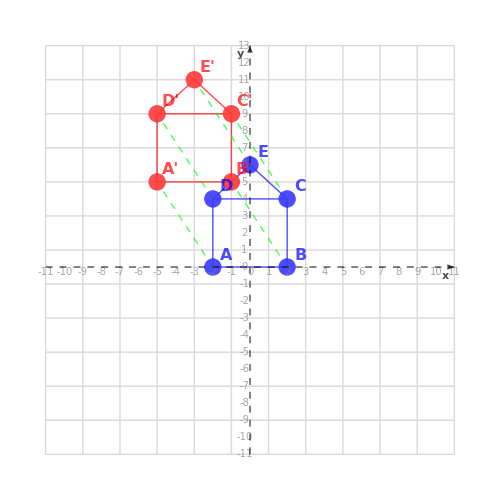

LEGENDA:

• Modré body a čiary: Pôvodný domček

• Červené body a čiary: Posunutý domček

• Zelené prerušované čiary: Posun jednotlivých vrcholov

• Mriežka: Súradnicový systém

Pôvodné vrcholy (modrá):

Vrchol 1: {-2,0}

Vrchol 2: {2,0}

Vrchol 3: {2,4}

Vrchol 4: {-2,4}

Vrchol 5: {0,6}

Výsledné vrcholy (červená):

Vrchol 1': {-5,5}

Vrchol 2': {-1,5}

Vrchol 3': {-1,9}

Vrchol 4': {-5,9}

Vrchol 5': {-3,11}

Inverzná transformácia:

Pre vrátenie do pôvodného stavu použite vektor posunu:

Δ' = [3, -5] (opačný vektor)

DRUHÁ TRANSFORMÁCIA: Rotácia

GEOMETRICKÉ TRANSFORMÁCIE DOMČEKA - ROTÁCIA

========================================

ZADANIE:

Majme domček s vrcholmi:

(-5 | 5
-1 | 5
-1 | 9
-5 | 9
-3 | 11)

Vykonajte rotáciu domčeka v 2D priestore okolo počiatku súradnicovej sústavy [0,0] o uhol α = 150°.

Transformačná matica rotácie:

(-(√3)/2 | -1/2
1/2 | -(√3)/2)

POSTUP:

Pre výpočet použijeme maticu rotácie:

Transformačná matica:

(cos(α) | -sin(α)
sin(α) | cos(α))

Naša hodnotu α = 150°:

cos(α) = -1/2 · √3

sin(α) = 1/2

Rotáciu vykonáme pomocou vzorcov:

x' = x · cos(α) - y · sin(α)

y' = x · sin(α) + y · cos(α)

Výpočet pre jednotlivé vrcholy:

Vrchol A:

Pôvodné súradnice: [-5, 5]

Výpočet x-ovej súradnice:

x' = x · cos(α) - y · sin(α)

x' = -5 · -1/2 · √3 - 5 · 1/2

x' = -5/2 + (5 · √3)/2

x' = -5/2 + (5 · √3)/2

Výpočet y-ovej súradnice:

y' = x · sin(α) + y · cos(α)

y' = -5 · 1/2 + 5 · -1/2 · √3

y' = -5/2 - (5 · √3)/2

y' = -5/2 - (5 · √3)/2

Výsledné súradnice: [-5/2 + (5 · √3)/2, -5/2 - (5 · √3)/2]

Overenie pomocou inverznej transformácie:

Pre inverzný uhol α' = -150°:

cos(α') = -1/2 · √3

sin(α') = -1/2

x = x' · cos(α') - y' · sin(α')

x = -5/2 + (5 · √3)/2 · -1/2 · √3 - -5/2 - (5 · √3)/2 · -1/2

x = -5

x = -5 = -5

y = x' · sin(α') + y' · cos(α')

y = -5/2 + (5 · √3)/2 · -1/2 + -5/2 - (5 · √3)/2 · -1/2 · √3

y = 5

y = 5 = 5

Maticový zápis:

(-(√3)/2 | -1/2
1/2 | -(√3)/2) · (-5
5) = (-5/2+(5 √3)/2
-5/2-(5 √3)/2)

Vrchol B:

Pôvodné súradnice: [-1, 5]

Výpočet x-ovej súradnice:

x' = x · cos(α) - y · sin(α)

x' = -1 · -1/2 · √3 - 5 · 1/2

x' = -5/2 + √3/2

x' = -5/2 + √3/2

Výpočet y-ovej súradnice:

y' = x · sin(α) + y · cos(α)

y' = -1 · 1/2 + 5 · -1/2 · √3

y' = -1/2 - (5 · √3)/2

y' = -1/2 - (5 · √3)/2

Výsledné súradnice: [-5/2 + √3/2, -1/2 - (5 · √3)/2]

Overenie pomocou inverznej transformácie:

Pre inverzný uhol α' = -150°:

cos(α') = -1/2 · √3

sin(α') = -1/2

x = x' · cos(α') - y' · sin(α')

x = -5/2 + √3/2 · -1/2 · √3 - -1/2 - (5 · √3)/2 · -1/2

x = -1

x = -1 = -1

y = x' · sin(α') + y' · cos(α')

y = -5/2 + √3/2 · -1/2 + -1/2 - (5 · √3)/2 · -1/2 · √3

y = 5

y = 5 = 5

Maticový zápis:

(-(√3)/2 | -1/2
1/2 | -(√3)/2) · (-1
5) = (-5/2+(√3)/2
-1/2-(5 √3)/2)

Vrchol C:

Pôvodné súradnice: [-1, 9]

Výpočet x-ovej súradnice:

x' = x · cos(α) - y · sin(α)

x' = -1 · -1/2 · √3 - 9 · 1/2

x' = -9/2 + √3/2

x' = -9/2 + √3/2

Výpočet y-ovej súradnice:

y' = x · sin(α) + y · cos(α)

y' = -1 · 1/2 + 9 · -1/2 · √3

y' = -1/2 - (9 · √3)/2

y' = -1/2 - (9 · √3)/2

Výsledné súradnice: [-9/2 + √3/2, -1/2 - (9 · √3)/2]

Overenie pomocou inverznej transformácie:

Pre inverzný uhol α' = -150°:

cos(α') = -1/2 · √3

sin(α') = -1/2

x = x' · cos(α') - y' · sin(α')

x = -9/2 + √3/2 · -1/2 · √3 - -1/2 - (9 · √3)/2 · -1/2

x = -1

x = -1 = -1

y = x' · sin(α') + y' · cos(α')

y = -9/2 + √3/2 · -1/2 + -1/2 - (9 · √3)/2 · -1/2 · √3

y = 9

y = 9 = 9

Maticový zápis:

(-(√3)/2 | -1/2
1/2 | -(√3)/2) · (-1
9) = (-9/2+(√3)/2
-1/2-(9 √3)/2)

Vrchol D:

Pôvodné súradnice: [-5, 9]

Výpočet x-ovej súradnice:

x' = x · cos(α) - y · sin(α)

x' = -5 · -1/2 · √3 - 9 · 1/2

x' = -9/2 + (5 · √3)/2

x' = -9/2 + (5 · √3)/2

Výpočet y-ovej súradnice:

y' = x · sin(α) + y · cos(α)

y' = -5 · 1/2 + 9 · -1/2 · √3

y' = -5/2 - (9 · √3)/2

y' = -5/2 - (9 · √3)/2

Výsledné súradnice: [-9/2 + (5 · √3)/2, -5/2 - (9 · √3)/2]

Overenie pomocou inverznej transformácie:

Pre inverzný uhol α' = -150°:

cos(α') = -1/2 · √3

sin(α') = -1/2

x = x' · cos(α') - y' · sin(α')

x = -9/2 + (5 · √3)/2 · -1/2 · √3 - -5/2 - (9 · √3)/2 · -1/2

x = -5

x = -5 = -5

y = x' · sin(α') + y' · cos(α')

y = -9/2 + (5 · √3)/2 · -1/2 + -5/2 - (9 · √3)/2 · -1/2 · √3

y = 9

y = 9 = 9

Maticový zápis:

(-(√3)/2 | -1/2
1/2 | -(√3)/2) · (-5
9) = (-9/2+(5 √3)/2
-5/2-(9 √3)/2)

Vrchol E:

Pôvodné súradnice: [-3, 11]

Výpočet x-ovej súradnice:

x' = x · cos(α) - y · sin(α)

x' = -3 · -1/2 · √3 - 11 · 1/2

x' = -11/2 + (3 · √3)/2

x' = -11/2 + (3 · √3)/2

Výpočet y-ovej súradnice:

y' = x · sin(α) + y · cos(α)

y' = -3 · 1/2 + 11 · -1/2 · √3

y' = -3/2 - (11 · √3)/2

y' = -3/2 - (11 · √3)/2

Výsledné súradnice: [-11/2 + (3 · √3)/2, -3/2 - (11 · √3)/2]

Overenie pomocou inverznej transformácie:

Pre inverzný uhol α' = -150°:

cos(α') = -1/2 · √3

sin(α') = -1/2

x = x' · cos(α') - y' · sin(α')

x = -11/2 + (3 · √3)/2 · -1/2 · √3 - -3/2 - (11 · √3)/2 · -1/2

x = -3

x = -3 = -3

y = x' · sin(α') + y' · cos(α')

y = -11/2 + (3 · √3)/2 · -1/2 + -3/2 - (11 · √3)/2 · -1/2 · √3

y = 11

y = 11 = 11

Maticový zápis:

(-(√3)/2 | -1/2
1/2 | -(√3)/2) · (-3
11) = (-11/2+(3 √3)/2
-3/2-(11 √3)/2)

VÝSLEDOK:

Vrcholy domčeka po rotácii:

(-5/2+(5 √3)/2 | -5/2-(5 √3)/2
-5/2+(√3)/2 | -1/2-(5 √3)/2
-9/2+(√3)/2 | -1/2-(9 √3)/2
-9/2+(5 √3)/2 | -5/2-(9 √3)/2
-11/2+(3 √3)/2 | -3/2-(11 √3)/2)

VIZUALIZÁCIA:

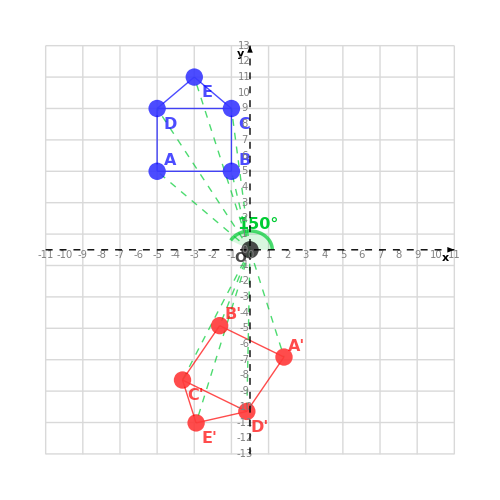

LEGENDA:

• Modré body a čiary: Pôvodný domček

• Červené body a čiary: Otočený domček

• Zelený oblúk: Znázornenie uhlu rotácie

• Zelené prerušované čiary: Spojenia vrcholov s počiatkom

• Mriežka: Súradnicový systém

• O: Počiatok súradnicovej sústavy - stred rotácie

Pôvodné vrcholy (modrá):

Vrchol A: {-5,5}

Vrchol B: {-1,5}

Vrchol C: {-1,9}

Vrchol D: {-5,9}

Vrchol E: {-3,11}

Výsledné vrcholy (červená):

Vrchol A': {-5/2+(5 √3)/2,-5/2-(5 √3)/2}

Vrchol B': {-5/2+(√3)/2,-1/2-(5 √3)/2}

Vrchol C': {-9/2+(√3)/2,-1/2-(9 √3)/2}

Vrchol D': {-9/2+(5 √3)/2,-5/2-(9 √3)/2}

Vrchol E': {-11/2+(3 √3)/2,-3/2-(11 √3)/2}

Inverzná transformácia:

Pre vrátenie do pôvodného stavu použite rotáciu o opačný uhol:

α' = -α = -150°

MATEMATICKÉ VLASTNOSTI:

• Rotácia okolo počiatku zachováva vzdialenosť všetkých bodov od počiatku sústavy [0,0]

• Rotácia nemení veľkosť ani tvar geometrických útvarov - je to izometria

• Rotácia zachováva uhly medzi úsečkami a ich dĺžky

• Rotácia zachováva obsah a obvod domčeka

• Počiatok súradnicovej sústavy [0,0] je fixný bod rotácie - zostáva nezmenený

TABUĽKA ŠPECIÁLNYCH HODNÔT:

Hodnoty pre najčastejšie uhly:

α | sin(α) | cos(α)
0° | 0 | 1
30° | 1/2 | √3/2
45° | 1/√2 | 1/√2
60° | √3/2 | 1/2
90° | 1 | 0
120° | √3/2 | -1/2
135° | 1/√2 | -1/√2
150° | 1/2 | -√3/2
180° | 0 | -1
270° | -1 | 0
360° | 0 | 1

TRETIA TRANSFORMÁCIA: Zväčšenie/Zmenšenie

GEOMETRICKÉ TRANSFORMÁCIE DOMČEKA - ZVÄČŠENIE/ZMENŠENIE

========================================

ZADANIE:

Majme domček s vrcholmi:

(-5/2+(5 √3)/2 | -5/2-(5 √3)/2
-5/2+(√3)/2 | -1/2-(5 √3)/2
-9/2+(√3)/2 | -1/2-(9 √3)/2
-9/2+(5 √3)/2 | -5/2-(9 √3)/2
-11/2+(3 √3)/2 | -3/2-(11 √3)/2)

Vykonajte zmenšenie domčeka v 2D priestore pomocou transformačnej matice:

(1/2 | 0
0 | 1/2)

POSTUP:

Pre výpočet použijeme maticu zmenšenie v tvare:

Transformačná matica:

(sx | 0
0 | sy)

kde:

sx je koeficient zmenšenie v smere osi x

sy je koeficient zmenšenie v smere osi y

V našom prípade:

sx = 1/2 (zmenšovanie v smere osi x)

sy = 1/2 (zmenšovanie v smere osi y)

Výpočet pre jednotlivé vrcholy:

Vrchol 1:

Pôvodné súradnice: [-5/2 + (5 · √3)/2, -5/2 - (5 · √3)/2]

Výpočet x-ovej súradnice:

x' = sx · x = 1/2 · -5/2 + (5 · √3)/2

x' = -5/4 + (5 · √3)/4

x' = (5 · (-1 + √3))/4

Výpočet y-ovej súradnice:

y' = sy · y = 1/2 · -5/2 - (5 · √3)/2

y' = -5/4 - (5 · √3)/4

y' = (-5 · (1 + √3))/4

Výsledné súradnice: [(5 · (-1 + √3))/4, (-5 · (1 + √3))/4]

Maticový zápis:

(1/2 | 0
0 | 1/2) · (-5/2+(5 √3)/2
-5/2-(5 √3)/2) = (5/4 (-1+√3)
-5/4 (1+√3))

Vrchol 2:

Pôvodné súradnice: [-5/2 + √3/2, -1/2 - (5 · √3)/2]

Výpočet x-ovej súradnice:

x' = sx · x = 1/2 · -5/2 + √3/2

x' = -5/4 + √3/4

x' = (-5 + √3)/4

Výpočet y-ovej súradnice:

y' = sy · y = 1/2 · -1/2 - (5 · √3)/2

y' = -1/4 - (5 · √3)/4

y' = (-1 - 5 · √3)/4

Výsledné súradnice: [(-5 + √3)/4, (-1 - 5 · √3)/4]

Maticový zápis:

(1/2 | 0
0 | 1/2) · (-5/2+(√3)/2
-1/2-(5 √3)/2) = (1/4 (-5+√3)
1/4 (-1-5 √3))

Vrchol 3:

Pôvodné súradnice: [-9/2 + √3/2, -1/2 - (9 · √3)/2]

Výpočet x-ovej súradnice:

x' = sx · x = 1/2 · -9/2 + √3/2

x' = -9/4 + √3/4

x' = (-9 + √3)/4

Výpočet y-ovej súradnice:

y' = sy · y = 1/2 · -1/2 - (9 · √3)/2

y' = -1/4 - (9 · √3)/4

y' = (-1 - 9 · √3)/4

Výsledné súradnice: [(-9 + √3)/4, (-1 - 9 · √3)/4]

Maticový zápis:

(1/2 | 0
0 | 1/2) · (-9/2+(√3)/2
-1/2-(9 √3)/2) = (1/4 (-9+√3)
1/4 (-1-9 √3))

Vrchol 4:

Pôvodné súradnice: [-9/2 + (5 · √3)/2, -5/2 - (9 · √3)/2]

Výpočet x-ovej súradnice:

x' = sx · x = 1/2 · -9/2 + (5 · √3)/2

x' = -9/4 + (5 · √3)/4

x' = (-9 + 5 · √3)/4

Výpočet y-ovej súradnice:

y' = sy · y = 1/2 · -5/2 - (9 · √3)/2

y' = -5/4 - (9 · √3)/4

y' = (-5 - 9 · √3)/4

Výsledné súradnice: [(-9 + 5 · √3)/4, (-5 - 9 · √3)/4]

Maticový zápis:

(1/2 | 0
0 | 1/2) · (-9/2+(5 √3)/2
-5/2-(9 √3)/2) = (1/4 (-9+5 √3)
1/4 (-5-9 √3))

Vrchol 5:

Pôvodné súradnice: [-11/2 + (3 · √3)/2, -3/2 - (11 · √3)/2]

Výpočet x-ovej súradnice:

x' = sx · x = 1/2 · -11/2 + (3 · √3)/2

x' = -11/4 + (3 · √3)/4

x' = (-11 + 3 · √3)/4

Výpočet y-ovej súradnice:

y' = sy · y = 1/2 · -3/2 - (11 · √3)/2

y' = -3/4 - (11 · √3)/4

y' = (-3 - 11 · √3)/4

Výsledné súradnice: [(-11 + 3 · √3)/4, (-3 - 11 · √3)/4]

Maticový zápis:

(1/2 | 0
0 | 1/2) · (-11/2+(3 √3)/2
-3/2-(11 √3)/2) = (1/4 (-11+3 √3)
1/4 (-3-11 √3))

VÝSLEDOK:

Vrcholy domčeka po zmenšenie:

(-5/4+(5 √3)/4 | -5/4-(5 √3)/4
-5/4+(√3)/4 | -1/4-(5 √3)/4
-9/4+(√3)/4 | -1/4-(9 √3)/4
-9/4+(5 √3)/4 | -5/4-(9 √3)/4
-11/4+(3 √3)/4 | -3/4-(11 √3)/4)

VIZUALIZÁCIA:

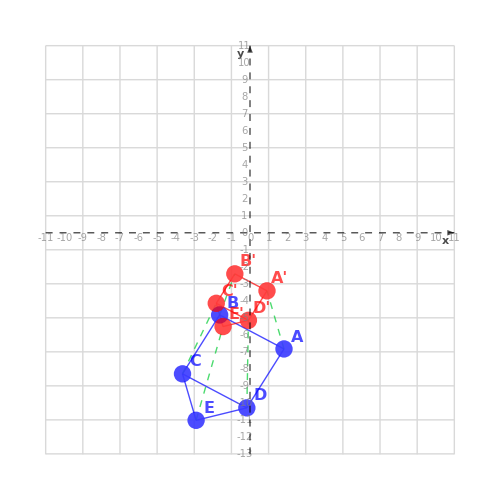

LEGENDA:

• Modré body a čiary: Pôvodný domček

• Červené body a čiary: Domček po zmenšenie

• Zelené prerušované čiary: Dráha zmeny veľkosti vrcholov

• Mriežka: Súradnicový systém

Pôvodné vrcholy (modrá):

Vrchol 1: {-5/2+(5 √3)/2,-5/2-(5 √3)/2}

Vrchol 2: {-5/2+(√3)/2,-1/2-(5 √3)/2}

Vrchol 3: {-9/2+(√3)/2,-1/2-(9 √3)/2}

Vrchol 4: {-9/2+(5 √3)/2,-5/2-(9 √3)/2}

Vrchol 5: {-11/2+(3 √3)/2,-3/2-(11 √3)/2}

Výsledné vrcholy (červená):

Vrchol 1': {-5/4+(5 √3)/4,-5/4-(5 √3)/4}

Vrchol 2': {-5/4+(√3)/4,-1/4-(5 √3)/4}

Vrchol 3': {-9/4+(√3)/4,-1/4-(9 √3)/4}

Vrchol 4': {-9/4+(5 √3)/4,-5/4-(9 √3)/4}

Vrchol 5': {-11/4+(3 √3)/4,-3/4-(11 √3)/4}

Inverzná transformácia:

Pre vrátenie do pôvodného stavu použite koeficienty:

sx' = 1/sx = 2 (zväčšovanie v smere osi x)

sy' = 1/sy = 2 (zväčšovanie v smere osi y)

MATEMATICKÉ VLASTNOSTI:

• Pri rovnakých koeficientoch (sx = sy = 1/2):

- Zachováva sa tvar (podobnosť) geometrických útvarov

- Zachovávajú sa všetky uhly medzi úsečkami

- Pomer dĺžok úsečiek sa zachováva

- Obsah domčeka sa zmenší na 4. časť

• Nemení sa poloha počiatku súradnicovej sústavy [0,0]

• Body, ktoré ležia na osi x, zostanú ležať na osi x (ich y-ová súradnica zostáva nulová)

• Body, ktoré ležia na osi y, zostanú ležať na osi y (ich x-ová súradnica zostáva nulová)

POSTUPNÝ VÝPOČET:

Pôvodný domček:

Vrcholy:

(-2 | 0
2 | 0
2 | 4
-2 | 4
0 | 6)

Vlastnosti domčeka:

Obsah: 20

Obvod: 21

Po prvej transformácii (Posun):

Vrcholy domčeka po prvej transformácii:

(-5 | 5
-1 | 5
-1 | 9
-5 | 9
-3 | 11)

Vlastnosti domčeka:

Obsah: 20

Obvod: 21

Po druhej transformácii (Rotácia):

Vrcholy domčeka po druhej transformácii:

(-5/2+(5 √3)/2 | -5/2-(5 √3)/2
-5/2+(√3)/2 | -1/2-(5 √3)/2
-9/2+(√3)/2 | -1/2-(9 √3)/2
-9/2+(5 √3)/2 | -5/2-(9 √3)/2
-11/2+(3 √3)/2 | -3/2-(11 √3)/2)

Vlastnosti domčeka:

Obsah: 25

Obvod: 21

Po tretej transformácii (Zväčšenie/Zmenšenie):

Vrcholy domčeka po tretej transformácii:

(-5/4+(5 √3)/4 | -5/4-(5 √3)/4
-5/4+(√3)/4 | -1/4-(5 √3)/4
-9/4+(√3)/4 | -1/4-(9 √3)/4
-9/4+(5 √3)/4 | -5/4-(9 √3)/4
-11/4+(3 √3)/4 | -3/4-(11 √3)/4)

Vlastnosti domčeka:

Obsah: 25

Obvod: 11

SÚHRNNÁ VIZUALIZÁCIA:

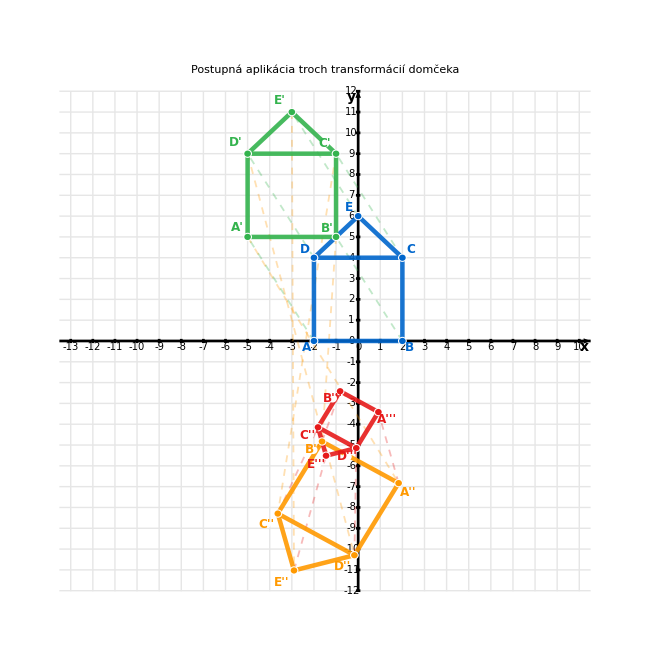

LEGENDA:

• Modré body a čiary: Pôvodný domček

• Tmavozelené body a čiary: Domček po prvej transformácii (Posun)

• Oranžové body a čiary: Domček po druhej transformácii (Rotácia)

• Červené body a čiary: Domček po tretej transformácii (Zväčšenie/Zmenšenie)

Postupnosť transformácií:

1. Posun

2. Rotácia

3. Zväčšenie/Zmenšenie

{{{-2,0},{2,0},{2,4},{-2,4},{0,6}},{{-5,5},{-1,5},{-1,9},{-5,9},{-3,11}},{{-5/2+(5 √3)/2,-5/2-(5 √3)/2},{-5/2+(√3)/2,-1/2-(5 √3)/2},{-9/2+(√3)/2,-1/2-(9 √3)/2},{-9/2+(5 √3)/2,-5/2-(9 √3)/2},{-11/2+(3 √3)/2,-3/2-(11 √3)/2}},{{5/4 (-1+√3),-5/4 (1+√3)},{1/4 (-5+√3),1/4 (-1-5 √3)},{1/4 (-9+√3),1/4 (-1-9 √3)},{1/4 (-9+5 √3),1/4 (-5-9 √3)},{1/4 (-11+3 √3),1/4 (-3-11 √3)}},Posun,Rotácia,Zväčšenie/Zmenšenie}

\nZADANIE:

Majme domček s vrcholmi:

(-4 | 1
4 | 1
4 | 4
-4 | 4
0 | 7)

Vykonajte zmenšenie domčeka pomocou transformačnej matice:

(1/(√5) | 0
0 | 1/(√5))

POSTUP:

Pre výpočet použijeme maticu zmenšenie v tvare:

Transformačná matica:

(sx | 0
0 | sy)

kde:

sx je koeficient zmenšenie v smere osi x

sy je koeficient zmenšenie v smere osi y

V našom prípade:

sx = 1/√5 (zmenšovanie v smere osi x)

sy = 1/√5 (zmenšovanie v smere osi y)

Výpočet pre jednotlivé vrcholy:

Vrchol 1:

Pôvodné súradnice: [-4, 1]

Výpočet x-ovej súradnice:

x' = sx · x = 1/√5 · -4

x' = -4/√5

x' = -4/√5

Výpočet y-ovej súradnice:

y' = sy · y = 1/√5 · 1

y' = 1/√5

y' = 1/√5

Výsledné súradnice: [-4/√5, 1/√5]

Maticový zápis:

(1/(√5) | 0
0 | 1/(√5)) · (-4
1) = (-4/(√5)
1/(√5))

Vrchol 2:

Pôvodné súradnice: [4, 1]

Výpočet x-ovej súradnice:

x' = sx · x = 1/√5 · 4

x' = 4/√5

x' = 4/√5

Výpočet y-ovej súradnice:

y' = sy · y = 1/√5 · 1

y' = 1/√5

y' = 1/√5

Výsledné súradnice: [4/√5, 1/√5]

Maticový zápis:

(1/(√5) | 0
0 | 1/(√5)) · (4
1) = (4/(√5)
1/(√5))

Vrchol 3:

Pôvodné súradnice: [4, 4]

Výpočet x-ovej súradnice:

x' = sx · x = 1/√5 · 4

x' = 4/√5

x' = 4/√5

Výpočet y-ovej súradnice:

y' = sy · y = 1/√5 · 4

y' = 4/√5

y' = 4/√5

Výsledné súradnice: [4/√5, 4/√5]

Maticový zápis:

(1/(√5) | 0
0 | 1/(√5)) · (4
4) = (4/(√5)
4/(√5))

Vrchol 4:

Pôvodné súradnice: [-4, 4]

Výpočet x-ovej súradnice:

x' = sx · x = 1/√5 · -4

x' = -4/√5

x' = -4/√5

Výpočet y-ovej súradnice:

y' = sy · y = 1/√5 · 4

y' = 4/√5

y' = 4/√5

Výsledné súradnice: [-4/√5, 4/√5]

Maticový zápis:

(1/(√5) | 0
0 | 1/(√5)) · (-4
4) = (-4/(√5)
4/(√5))

Vrchol 5:

Pôvodné súradnice: [0, 7]

Výpočet x-ovej súradnice:

x' = sx · x = 1/√5 · 0

x' = 0

Výpočet y-ovej súradnice:

y' = sy · y = 1/√5 · 7

y' = 7/√5

y' = 7/√5

Výsledné súradnice: [0, 7/√5]

Maticový zápis:

(1/(√5) | 0
0 | 1/(√5)) · (0
7) = (0
7/(√5))

VÝSLEDOK:

Vrcholy domčeka po zmenšenie:

(-4/(√5) | 1/(√5)
4/(√5) | 1/(√5)
4/(√5) | 4/(√5)
-4/(√5) | 4/(√5)
0 | 7/(√5))

VIZUALIZÁCIA:

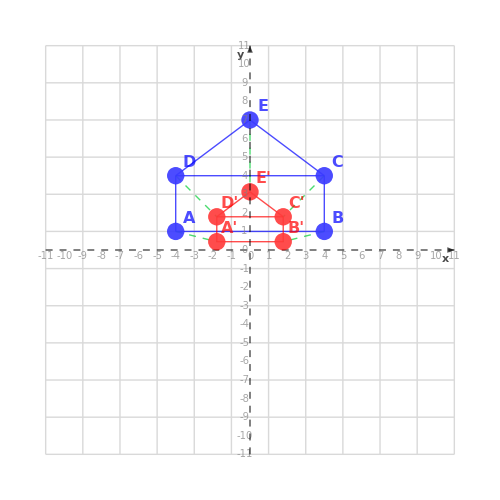

LEGENDA:

• Modré body a čiary: Pôvodný domček

• Červené body a čiary: Domček po zmenšenie

• Zelené prerušované čiary: Dráha zmeny veľkosti vrcholov

• Mriežka: Súradnicový systém

Pôvodné vrcholy (modrá):

Vrchol 1: {-4,1}

Vrchol 2: {4,1}

Vrchol 3: {4,4}

Vrchol 4: {-4,4}

Vrchol 5: {0,7}

Výsledné vrcholy (červená):

Vrchol 1': {-4/(√5),1/(√5)}

Vrchol 2': {4/(√5),1/(√5)}

Vrchol 3': {4/(√5),4/(√5)}

Vrchol 4': {-4/(√5),4/(√5)}

Vrchol 5': {0,7/(√5)}

Inverzná transformácia:

Pre vrátenie do pôvodného stavu použite koeficienty:

sx' = 1/sx = √5 (zväčšovanie v smere osi x)

sy' = 1/sy = √5 (zväčšovanie v smere osi y)

MATEMATICKÉ VLASTNOSTI:

• Pri rovnakých koeficientoch (sx = sy = 1/√5):

- Zachováva sa tvar (podobnosť) geometrických útvarov

- Zachovávajú sa všetky uhly medzi úsečkami

- Pomer dĺžok úsečiek sa zachováva

- Obsah domčeka sa zmenší na 5. časť

• Nemení sa poloha počiatku súradnicovej sústavy [0,0]

• Body, ktoré ležia na osi x, zostanú ležať na osi x (ich y-ová súradnica zostáva nulová)

• Body, ktoré ležia na osi y, zostanú ležať na osi y (ich x-ová súradnica zostáva nulová)

DRUHÁ TRANSFORMÁCIA: Posun

GEOMETRICKÉ TRANSFORMÁCIE DOMČEKA - POSUN

========================================

ZADANIE:

Majme domček s vrcholmi:

(-4/(√5) | 1/(√5)
4/(√5) | 1/(√5)
4/(√5) | 4/(√5)
-4/(√5) | 4/(√5)
0 | 7/(√5))

Vykonajte posun domčeka pomocou vektora posunu: Δ = [-4, -2]

Transformačná matica posunu v homogénnych súradniciach:

(1 | 0 | -4
0 | 1 | -2
0 | 0 | 1)

POSTUP:

Pre výpočet použijeme maticu posunu v homogénnych súradniciach:

Transformačná matica:

(1 | 0 | dx
0 | 1 | dy
0 | 0 | 1)

Pre naše hodnoty:

dx = -4

dy = -2

Posun vykonáme pomocou vzorcov:

x' = x + dx

y' = y + dy

Výpočet pre jednotlivé vrcholy:

Vrchol 1:

Pôvodné súradnice: [-4/(√5), 1/(√5)]

Výpočet x-ovej súradnice:

x' = x + dx = -4/(√5) + -4

x' = -4-4/(√5)

Výpočet y-ovej súradnice:

y' = y + dy = 1/(√5) + -2

y' = -2+1/(√5)

Overenie pomocou inverznej transformácie:

x = x' + (-dx) = -4-4/(√5) + (4) = -4/(√5)

y = y' + (-dy) = -2+1/(√5) + (2) = 1/(√5)

Maticový zápis:

(1 | 0 | -4
0 | 1 | -2
0 | 0 | 1) · (-4/(√5)
1/(√5)
1) = (-4-4/(√5)
-2+1/(√5)
1)

Vrchol 2:

Pôvodné súradnice: [4/(√5), 1/(√5)]

Výpočet x-ovej súradnice:

x' = x + dx = 4/(√5) + -4

x' = -4+4/(√5)

Výpočet y-ovej súradnice:

y' = y + dy = 1/(√5) + -2

y' = -2+1/(√5)

Overenie pomocou inverznej transformácie:

x = x' + (-dx) = -4+4/(√5) + (4) = 4/(√5)

y = y' + (-dy) = -2+1/(√5) + (2) = 1/(√5)

Maticový zápis:

(1 | 0 | -4
0 | 1 | -2
0 | 0 | 1) · (4/(√5)
1/(√5)
1) = (-4+4/(√5)
-2+1/(√5)
1)

Vrchol 3:

Pôvodné súradnice: [4/(√5), 4/(√5)]

Výpočet x-ovej súradnice:

x' = x + dx = 4/(√5) + -4

x' = -4+4/(√5)

Výpočet y-ovej súradnice:

y' = y + dy = 4/(√5) + -2

y' = -2+4/(√5)

Overenie pomocou inverznej transformácie:

x = x' + (-dx) = -4+4/(√5) + (4) = 4/(√5)

y = y' + (-dy) = -2+4/(√5) + (2) = 4/(√5)

Maticový zápis:

(1 | 0 | -4
0 | 1 | -2
0 | 0 | 1) · (4/(√5)
4/(√5)
1) = (-4+4/(√5)
-2+4/(√5)
1)

Vrchol 4:

Pôvodné súradnice: [-4/(√5), 4/(√5)]

Výpočet x-ovej súradnice:

x' = x + dx = -4/(√5) + -4

x' = -4-4/(√5)

Výpočet y-ovej súradnice:

y' = y + dy = 4/(√5) + -2

y' = -2+4/(√5)

Overenie pomocou inverznej transformácie:

x = x' + (-dx) = -4-4/(√5) + (4) = -4/(√5)

y = y' + (-dy) = -2+4/(√5) + (2) = 4/(√5)

Maticový zápis:

(1 | 0 | -4
0 | 1 | -2
0 | 0 | 1) · (-4/(√5)
4/(√5)
1) = (-4-4/(√5)
-2+4/(√5)
1)

Vrchol 5:

Pôvodné súradnice: [0, 7/(√5)]

Výpočet x-ovej súradnice:

x' = x + dx = 0 + -4

x' = -4

Výpočet y-ovej súradnice:

y' = y + dy = 7/(√5) + -2

y' = -2+7/(√5)

Overenie pomocou inverznej transformácie:

x = x' + (-dx) = -4 + (4) = 0

y = y' + (-dy) = -2+7/(√5) + (2) = 7/(√5)

Maticový zápis:

(1 | 0 | -4
0 | 1 | -2
0 | 0 | 1) · (0
7/(√5)
1) = (-4
-2+7/(√5)
1)

VÝSLEDOK:

Vrcholy domčeka po posune:

(-4-4/(√5) | -2+1/(√5)
-4+4/(√5) | -2+1/(√5)
-4+4/(√5) | -2+4/(√5)
-4-4/(√5) | -2+4/(√5)
-4 | -2+7/(√5))

VIZUALIZÁCIA:

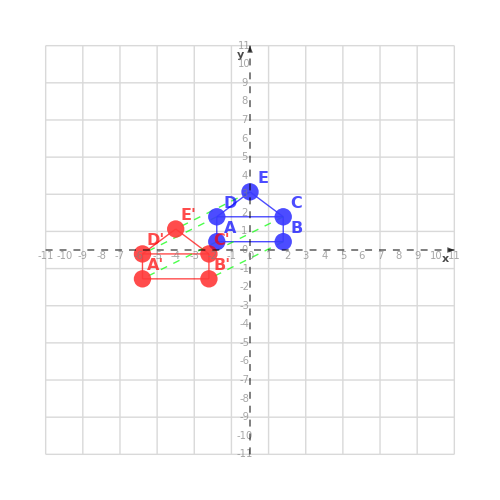

LEGENDA:

• Modré body a čiary: Pôvodný domček

• Červené body a čiary: Posunutý domček

• Zelené prerušované čiary: Posun jednotlivých vrcholov

• Mriežka: Súradnicový systém

Pôvodné vrcholy (modrá):

Vrchol 1: {-4/(√5),1/(√5)}

Vrchol 2: {4/(√5),1/(√5)}

Vrchol 3: {4/(√5),4/(√5)}

Vrchol 4: {-4/(√5),4/(√5)}

Vrchol 5: {0,7/(√5)}

Výsledné vrcholy (červená):

Vrchol 1': {-4-4/(√5),-2+1/(√5)}

Vrchol 2': {-4+4/(√5),-2+1/(√5)}

Vrchol 3': {-4+4/(√5),-2+4/(√5)}

Vrchol 4': {-4-4/(√5),-2+4/(√5)}

Vrchol 5': {-4,-2+7/(√5)}

Inverzná transformácia:

Pre vrátenie do pôvodného stavu použite vektor posunu:

Δ' = [4, 2] (opačný vektor)

TRETIA TRANSFORMÁCIA: Rotácia

GEOMETRICKÉ TRANSFORMÁCIE DOMČEKA - ROTÁCIA

========================================

ZADANIE:

Majme domček s vrcholmi:

(-4/5 (5+√5) | -2+1/(√5)
-4+4/(√5) | -2+1/(√5)
-4+4/(√5) | -2+4/(√5)
-4/5 (5+√5) | -2+4/(√5)
-4 | -2+7/(√5))

Vykonajte rotáciu domčeka okolo počiatku súradnicovej sústavy [0,0] o uhol α = 150°.

Transformačná matica rotácie:

(-(√3)/2 | -1/2
1/2 | -(√3)/2)

POSTUP:

Pre výpočet použijeme maticu rotácie:

Transformačná matica:

(cos(α) | -sin(α)
sin(α) | cos(α))

Naša hodnotu α = 150°:

cos(α) = -1/2 · √3

sin(α) = 1/2

Rotáciu vykonáme pomocou vzorcov:

x' = x · cos(α) - y · sin(α)

y' = x · sin(α) + y · cos(α)

Výpočet pre jednotlivé vrcholy:

Vrchol A:

Pôvodné súradnice: [(-4 · (5 + √5))/5, -2 + 1/√5]

Výpočet x-ovej súradnice:

x' = x · cos(α) - y · sin(α)

x' = (-4 · (5 + √5))/5 · -1/2 · √3 - -2 + 1/√5 · 1/2

x' = 1 + 2 · √3/5] + 2*Sqrt[3] - 1/(2*Sqrt[5)

x' = 1 + 2 · √3/5] + 2*Sqrt[3] - 1/(2*Sqrt[5)

Výpočet y-ovej súradnice:

y' = x · sin(α) + y · cos(α)

y' = (-4 · (5 + √5))/5 · 1/2 + -2 + 1/√5 · -1/2 · √3

y' = -2 - √3/5]/2 + Sqrt[3] - 2/Sqrt[5

y' = -2 - √3/5]/2 + Sqrt[3] - 2/Sqrt[5

Výsledné súradnice: [1 + 2 · √3/5] + 2*Sqrt[3] - 1/(2*Sqrt[5), -2 - √3/5]/2 + Sqrt[3] - 2/Sqrt[5]

Overenie pomocou inverznej transformácie:

Pre inverzný uhol α' = -150°:

cos(α') = -1/2 · √3

sin(α') = -1/2

x = x' · cos(α') - y' · sin(α')

x = 1 + 2 · √3/5] + 2*Sqrt[3] - 1/(2*Sqrt[5) · -1/2 · √3 - -2 - √3/5]/2 + Sqrt[3] - 2/Sqrt[5 · -1/2

x = -4 - 4/√5

x = (-4 · (5 + √5))/5 = (-4 · (5 + √5))/5

y = x' · sin(α') + y' · cos(α')

y = 1 + 2 · √3/5] + 2*Sqrt[3] - 1/(2*Sqrt[5) · -1/2 + -2 - √3/5]/2 + Sqrt[3] - 2/Sqrt[5 · -1/2 · √3

y = -2 + 1/√5

y = -2 + 1/√5 = -2 + 1/√5

Maticový zápis:

(-(√3)/2 | -1/2
1/2 | -(√3)/2) · (-4/5 (5+√5)
-2+1/(√5)) = (1+2 √(3/5)+2 √3-1/(2 √5)
-2-(√(3/5))/2+√3-2/(√5))

Vrchol B:

Pôvodné súradnice: [-4 + 4/√5, -2 + 1/√5]

Výpočet x-ovej súradnice:

x' = x · cos(α) - y · sin(α)

x' = -4 + 4/√5 · -1/2 · √3 - -2 + 1/√5 · 1/2

x' = 1 - 2 · √3/5] + 2*Sqrt[3] - 1/(2*Sqrt[5)

x' = 1 - 2 · √3/5] + 2*Sqrt[3] - 1/(2*Sqrt[5)

Výpočet y-ovej súradnice:

y' = x · sin(α) + y · cos(α)

y' = -4 + 4/√5 · 1/2 + -2 + 1/√5 · -1/2 · √3

y' = -2 - √3/5]/2 + Sqrt[3] + 2/Sqrt[5

y' = -2 - √3/5]/2 + Sqrt[3] + 2/Sqrt[5

Výsledné súradnice: [1 - 2 · √3/5] + 2*Sqrt[3] - 1/(2*Sqrt[5), -2 - √3/5]/2 + Sqrt[3] + 2/Sqrt[5]

Overenie pomocou inverznej transformácie:

Pre inverzný uhol α' = -150°:

cos(α') = -1/2 · √3

sin(α') = -1/2

x = x' · cos(α') - y' · sin(α')

x = 1 - 2 · √3/5] + 2*Sqrt[3] - 1/(2*Sqrt[5) · -1/2 · √3 - -2 - √3/5]/2 + Sqrt[3] + 2/Sqrt[5 · -1/2

x = -4 + 4/√5

x = -4 + 4/√5 = -4 + 4/√5

y = x' · sin(α') + y' · cos(α')

y = 1 - 2 · √3/5] + 2*Sqrt[3] - 1/(2*Sqrt[5) · -1/2 + -2 - √3/5]/2 + Sqrt[3] + 2/Sqrt[5 · -1/2 · √3

y = -2 + 1/√5

y = -2 + 1/√5 = -2 + 1/√5

Maticový zápis:

(-(√3)/2 | -1/2
1/2 | -(√3)/2) · (-4+4/(√5)
-2+1/(√5)) = (1-2 √(3/5)+2 √3-1/(2 √5)
-2-(√(3/5))/2+√3+2/(√5))

Vrchol C:

Pôvodné súradnice: [-4 + 4/√5, -2 + 4/√5]

Výpočet x-ovej súradnice:

x' = x · cos(α) - y · sin(α)

x' = -4 + 4/√5 · -1/2 · √3 - -2 + 4/√5 · 1/2

x' = 1 - 2 · √3/5] + 2*Sqrt[3] - 2/Sqrt[5

x' = 1 - 2 · √3/5] + 2*Sqrt[3] - 2/Sqrt[5

Výpočet y-ovej súradnice:

y' = x · sin(α) + y · cos(α)

y' = -4 + 4/√5 · 1/2 + -2 + 4/√5 · -1/2 · √3

y' = -2 - 2 · √3/5] + Sqrt[3] + 2/Sqrt[5

y' = -2 - 2 · √3/5] + Sqrt[3] + 2/Sqrt[5

Výsledné súradnice: [1 - 2 · √3/5] + 2*Sqrt[3] - 2/Sqrt[5, -2 - 2 · √3/5] + Sqrt[3] + 2/Sqrt[5]

Overenie pomocou inverznej transformácie:

Pre inverzný uhol α' = -150°:

cos(α') = -1/2 · √3

sin(α') = -1/2

x = x' · cos(α') - y' · sin(α')

x = 1 - 2 · √3/5] + 2*Sqrt[3] - 2/Sqrt[5 · -1/2 · √3 - -2 - 2 · √3/5] + Sqrt[3] + 2/Sqrt[5 · -1/2

x = -4 + 4/√5

x = -4 + 4/√5 = -4 + 4/√5

y = x' · sin(α') + y' · cos(α')

y = 1 - 2 · √3/5] + 2*Sqrt[3] - 2/Sqrt[5 · -1/2 + -2 - 2 · √3/5] + Sqrt[3] + 2/Sqrt[5 · -1/2 · √3

y = -2 + 4/√5

y = -2 + 4/√5 = -2 + 4/√5

Maticový zápis:

(-(√3)/2 | -1/2
1/2 | -(√3)/2) · (-4+4/(√5)
-2+4/(√5)) = (1-2 √(3/5)+2 √3-2/(√5)
-2-2 √(3/5)+√3+2/(√5))

Vrchol D:

Pôvodné súradnice: [(-4 · (5 + √5))/5, -2 + 4/√5]

Výpočet x-ovej súradnice:

x' = x · cos(α) - y · sin(α)

x' = (-4 · (5 + √5))/5 · -1/2 · √3 - -2 + 4/√5 · 1/2

x' = 1 + 2 · √3/5] + 2*Sqrt[3] - 2/Sqrt[5

x' = 1 + 2 · √3/5] + 2*Sqrt[3] - 2/Sqrt[5

Výpočet y-ovej súradnice:

y' = x · sin(α) + y · cos(α)

y' = (-4 · (5 + √5))/5 · 1/2 + -2 + 4/√5 · -1/2 · √3

y' = -2 - 2 · √3/5] + Sqrt[3] - 2/Sqrt[5

y' = -2 - 2 · √3/5] + Sqrt[3] - 2/Sqrt[5

Výsledné súradnice: [1 + 2 · √3/5] + 2*Sqrt[3] - 2/Sqrt[5, -2 - 2 · √3/5] + Sqrt[3] - 2/Sqrt[5]

Overenie pomocou inverznej transformácie:

Pre inverzný uhol α' = -150°:

cos(α') = -1/2 · √3

sin(α') = -1/2

x = x' · cos(α') - y' · sin(α')

x = 1 + 2 · √3/5] + 2*Sqrt[3] - 2/Sqrt[5 · -1/2 · √3 - -2 - 2 · √3/5] + Sqrt[3] - 2/Sqrt[5 · -1/2

x = -4 - 4/√5

x = (-4 · (5 + √5))/5 = (-4 · (5 + √5))/5

y = x' · sin(α') + y' · cos(α')

y = 1 + 2 · √3/5] + 2*Sqrt[3] - 2/Sqrt[5 · -1/2 + -2 - 2 · √3/5] + Sqrt[3] - 2/Sqrt[5 · -1/2 · √3

y = -2 + 4/√5

y = -2 + 4/√5 = -2 + 4/√5

Maticový zápis:

(-(√3)/2 | -1/2
1/2 | -(√3)/2) · (-4/5 (5+√5)
-2+4/(√5)) = (1+2 √(3/5)+2 √3-2/(√5)
-2-2 √(3/5)+√3-2/(√5))

Vrchol E:

Pôvodné súradnice: [-4, -2 + 7/√5]

Výpočet x-ovej súradnice:

x' = x · cos(α) - y · sin(α)

x' = -4 · -1/2 · √3 - -2 + 7/√5 · 1/2

x' = 1 + 2 · √3] - 7/(2*Sqrt[5)

x' = 1 + 2 · √3] - 7/(2*Sqrt[5)

Výpočet y-ovej súradnice:

y' = x · sin(α) + y · cos(α)

y' = -4 · 1/2 + -2 + 7/√5 · -1/2 · √3

y' = -2 - (7 · √3/5])/2 + Sqrt[3

y' = -2 - (7 · √3/5])/2 + Sqrt[3

Výsledné súradnice: [1 + 2 · √3] - 7/(2*Sqrt[5), -2 - (7 · √3/5])/2 + Sqrt[3]

Overenie pomocou inverznej transformácie:

Pre inverzný uhol α' = -150°:

cos(α') = -1/2 · √3

sin(α') = -1/2

x = x' · cos(α') - y' · sin(α')

x = 1 + 2 · √3] - 7/(2*Sqrt[5) · -1/2 · √3 - -2 - (7 · √3/5])/2 + Sqrt[3 · -1/2

x = -4

x = -4 = -4

y = x' · sin(α') + y' · cos(α')

y = 1 + 2 · √3] - 7/(2*Sqrt[5) · -1/2 + -2 - (7 · √3/5])/2 + Sqrt[3 · -1/2 · √3

y = -2 + 7/√5

y = -2 + 7/√5 = -2 + 7/√5

Maticový zápis:

(-(√3)/2 | -1/2
1/2 | -(√3)/2) · (-4
-2+7/(√5)) = (1+2 √3-7/(2 √5)
-2-(7 √(3/5))/2+√3)

VÝSLEDOK:

Vrcholy domčeka po rotácii:

(1+2 √(3/5)+2 √3-1/(2 √5) | -2-(√(3/5))/2+√3-2/(√5)
1-2 √(3/5)+2 √3-1/(2 √5) | -2-(√(3/5))/2+√3+2/(√5)
1-2 √(3/5)+2 √3-2/(√5) | -2-2 √(3/5)+√3+2/(√5)
1+2 √(3/5)+2 √3-2/(√5) | -2-2 √(3/5)+√3-2/(√5)
1+2 √3-7/(2 √5) | -2-(7 √(3/5))/2+√3)

VIZUALIZÁCIA:

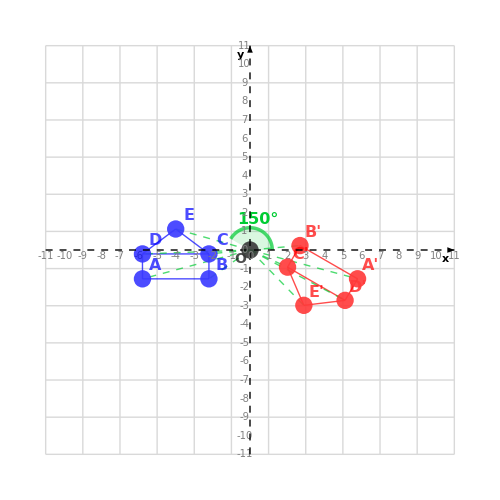

LEGENDA:

"• Modré body a čiary: Pôvodný domček

• Červené body a čiary: Otočený domček

• Zelený oblúk: Znázornenie uhlu rotácie

• Zelené prerušované čiary: Spojenia vrcholov s počiatkom

• Mriežka: Súradnicový systém

• O: Počiatok súradnicovej sústavy - stred rotácie

Pôvodné vrcholy (modrá):

Vrchol A: {-4/5 (5+√5),-2+1/(√5)}

Vrchol B: {-4+4/(√5),-2+1/(√5)}

Vrchol C: {-4+4/(√5),-2+4/(√5)}

Vrchol D: {-4/5 (5+√5),-2+4/(√5)}

Vrchol E: {-4,-2+7/(√5)}

Výsledné vrcholy (červená):

Vrchol A': {1+2 √(3/5)+2 √3-1/(2 √5),-2-(√(3/5))/2+√3-2/(√5)}

Vrchol B': {1-2 √(3/5)+2 √3-1/(2 √5),-2-(√(3/5))/2+√3+2/(√5)}

Vrchol C': {1-2 √(3/5)+2 √3-2/(√5),-2-2 √(3/5)+√3+2/(√5)}

Vrchol D': {1+2 √(3/5)+2 √3-2/(√5),-2-2 √(3/5)+√3-2/(√5)}

Vrchol E': {1+2 √3-7/(2 √5),-2-(7 √(3/5))/2+√3}

Inverzná transformácia:

Pre vrátenie do pôvodného stavu použite rotáciu o opačný uhol:

α' = -α = -150°

MATEMATICKÉ VLASTNOSTI:

• Rotácia okolo počiatku zachováva vzdialenosť všetkých bodov od počiatku sústavy [0,0]

• Rotácia nemení veľkosť ani tvar geometrických útvarov - je to izometria

• Rotácia zachováva uhly medzi úsečkami a ich dĺžky

• Rotácia zachováva obsah a obvod domčeka

• Počiatok súradnicovej sústavy [0,0] je fixný bod rotácie - zostáva nezmenený

TABUĽKA ŠPECIÁLNYCH HODNÔT:

Hodnoty pre najčastejšie uhly:

α | sin(α) | cos(α)
0° | 0 | 1
30° | 1/2 | √3/2
45° | 1/√2 | 1/√2
60° | √3/2 | 1/2
90° | 1 | 0
120° | √3/2 | -1/2
135° | 1/√2 | -1/√2
150° | 1/2 | -√3/2
180° | 0 | -1
270° | -1 | 0
360° | 0 | 1

POSTUPNÝ VÝPOČET:

Pôvodný domček:

Vrcholy:

(-4 | 1
4 | 1
4 | 4
-4 | 4
0 | 7)

Vlastnosti domčeka:

Obsah: 30

Obvod: 31

Po prvej transformácii (Zväčšenie/Zmenšenie):

Vrcholy domčeka po prvej transformácii:

(-4/(√5) | 1/(√5)
4/(√5) | 1/(√5)
4/(√5) | 4/(√5)
-4/(√5) | 4/(√5)
0 | 7/(√5))

Vlastnosti domčeka:

Obsah: 6

Obvod: 14

Po druhej transformácii (Posun):

Vrcholy domčeka po druhej transformácii:

(-4-4/(√5) | -2+1/(√5)
-4+4/(√5) | -2+1/(√5)
-4+4/(√5) | -2+4/(√5)
-4-4/(√5) | -2+4/(√5)
-4 | -2+7/(√5))

Vlastnosti domčeka:

Obsah: 25

Obvod: 14

Po tretej transformácii (Rotácia):

Vrcholy domčeka po tretej transformácii:

(1+2 √(3/5)+2 √3-1/(2 √5) | -2-(√(3/5))/2+√3-2/(√5)
1-2 √(3/5)+2 √3-1/(2 √5) | -2-(√(3/5))/2+√3+2/(√5)
1-2 √(3/5)+2 √3-2/(√5) | -2-2 √(3/5)+√3+2/(√5)
1+2 √(3/5)+2 √3-2/(√5) | -2-2 √(3/5)+√3-2/(√5)
1+2 √3-7/(2 √5) | -2-(7 √(3/5))/2+√3)

Vlastnosti domčeka:

Obsah: 25

Obvod: 14

SÚHRNNÁ VIZUALIZÁCIA:

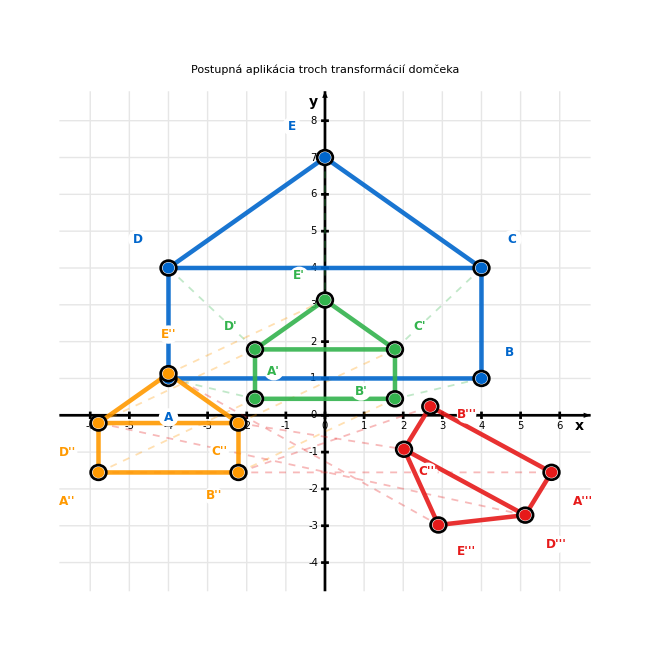

LEGENDA:

• Modré body a čiary: Pôvodný domček

• Tmavozelené body a čiary: Domček po prvej transformácii (Zväčšenie/Zmenšenie)

• Oranžové body a čiary: Domček po druhej transformácii (Posun)

• Červené body a čiary: Domček po tretej transformácii (Rotácia)

Postupnosť transformácií:

1. Zväčšenie/Zmenšenie

2. Posun

3. Rotácia

{{{-4,1},{4,1},{4,4},{-4,4},{0,7}},{{-4/(√5),1/(√5)},{4/(√5),1/(√5)},{4/(√5),4/(√5)},{-4/(√5),4/(√5)},{0,7/(√5)}},{{-4-4/(√5),-2+1/(√5)},{-4+4/(√5),-2+1/(√5)},{-4+4/(√5),-2+4/(√5)},{-4-4/(√5),-2+4/(√5)},{-4,-2+7/(√5)}},{{1+2 √(3/5)+2 √3-1/(2 √5),-2-(√(3/5))/2+√3-2/(√5)},{1-2 √(3/5)+2 √3-1/(2 √5),-2-(√(3/5))/2+√3+2/(√5)},{1-2 √(3/5)+2 √3-2/(√5),-2-2 √(3/5)+√3+2/(√5)},{1+2 √(3/5)+2 √3-2/(√5),-2-2 √(3/5)+√3-2/(√5)},{1+2 √3-7/(2 √5),-2-(7 √(3/5))/2+√3}},Zväčšenie/Zmenšenie,Posun,Rotácia}

```mathematica
DomcekTrojitaTransformacia[]
```